```mathematica
H=1/(2I1)(pα-pγ Cos[β])^2/Sin[β]^2+1/(2I1)pβ^2+1/(2I3)pγ^2+m g l Cos[β]
```

pβ^2/(2 I1)+pγ^2/(2 I3)+g l m Cos[β]+((pα-pγ Cos[β])^2 Csc[β]^2)/(2 I1)

```mathematica
-D[H, α]
-D[H, β]//FullSimplify//TrigExpand//FullSimplify
-D[H, γ]
D[H, pγ]//TrigExpand//FullSimplify
```

0

((-pγ+pα Cos[β]) (pα-pγ Cos[β]) Csc[β]^3)/I1+g l m Sin[β]

0

pγ/I3+((-pα+pγ Cos[β]) Cot[β] Csc[β])/I1

```mathematica
f=2I1 En-I1/I3 pγ^2-(pα-pγ Cos[β])^2/Sin[β]^2-2I1 m g l Cos[β]
```

2 En I1-(I1 pγ^2)/I3-2 g I1 l m Cos[β]-(pα-pγ Cos[β])^2 Csc[β]^2

```mathematica
D[√f, En]
D[√f, pα]//FullSimplify
D[√f, pγ]//FullSimplify
```

I1/(√(2 En I1-(I1 pγ^2)/I3-2 g I1 l m Cos[β]-(pα-pγ Cos[β])^2 Csc[β]^2))

((-pα+pγ Cos[β]) Csc[β]^2)/(√(2 En I1-(I1 pγ^2)/I3-2 g I1 l m Cos[β]-(pγ Cot[β]-pα Csc[β])^2))

(-pγ (I1+I3 Cot[β]^2)+I3 pα Cot[β] Csc[β])/(I3 √(2 En I1-(I1 pγ^2)/I3-2 g I1 l m Cos[β]-(pγ Cot[β]-pα Csc[β])^2))

```mathematica
√f/.{Cos[β]->ζ,Csc[β]->1/(√(1-ζ^2))}//FullSimplify
%/(√(1-ζ^2))//ExpandAll
-∫%ⅆζ
```

√(2 En I1-(I1 (pγ^2+2 g I3 l m ζ))/I3+(pα-pγ ζ)^2/(-1+ζ^2))

(√(2 En I1-(I1 pγ^2)/I3-2 g I1 l m ζ+pα^2/(-1+ζ^2)-(2 pα pγ ζ)/(-1+ζ^2)+(pγ^2 ζ^2)/(-1+ζ^2)))/(√(1-ζ^2))

-∫(√(2 En I1-(I1 pγ^2)/I3-2 g I1 l m ζ+pα^2/(-1+ζ^2)-(2 pα pγ ζ)/(-1+ζ^2)+(pγ^2 ζ^2)/(-1+ζ^2)))/(√(1-ζ^2))ⅆζ

```mathematica
$Assumptions={I1∈Reals,m∈Reals,g∈Reals,l∈Reals,I3∈Reals,pγ∈Reals,pα∈Reals,En∈Reals,β∈Reals};
S=-En t+α pα+γ pγ+∫√f ⅆβ
```

```mathematica
βEn=D[S, En]
```

```mathematica
βEn/.{I1->1,m->1,g->1,l->1,I3->1/2,pγ->2,pα->1,En->9/2}/.{β->1.4}
```

(-0.632147-2.15652 ⅈ)-t

```mathematica
params={I1->1,m->1,g->1,l->1,I3->1/2,pγ->2,pα->1,En->9/2};

fEq[β_]:=(2 I1 En-(I1/I3) pγ^2-(pα-pγ Cos[β])^2/Sin[β]^2-2 I1 m g l Cos[β])/. params

βEq[β_?NumericQ]:=NIntegrate[1/Sqrt[fEq[βp]],{βp,π/3,β}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in βp near {βp} = {1.047197551196598563257924413556215673208580707831240347253768698}. NIntegrate obtained 0.00496767-8.48282×10^-9 ⅈ and 1.18753×10^-8 for the integral and error estimates.

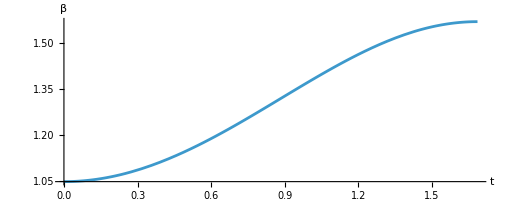

```mathematica
ParametricPlot[{Re[βEq[β]],β},{β,π/3,π/2},AxesLabel->{"t","β"},PlotRange->All]
```

```mathematica
$Assumptions={En∈Reals,m∈Reals,c∈Reals,r∈Reals,α∈Reals,M∈Reals,M>0,A∈Reals,A<0,B∈Reals,F∈Reals,F<0,r>0};
Solve[A r^2+B r + F==0,r]
```

{{r→ConditionalExpression[-B/(2 A)+(√(B^2-4 A F))/(2 A), B^2/(4 F)<A&&B>0]},{r→ConditionalExpression[-B/(2 A)-(√(B^2-4 A F))/(2 A), B^2/(4 F)<A&&B>0]}}

```mathematica
(-B/(2 A)+(√(B^2-4 A F))/(2 A))(-B/(2 A)-(√(B^2-4 A F))/(2 A))//FullSimplify
```

F/A

```mathematica
Δϕ=Assuming[B^2/(4 F)<A,2∫(c M)/(√(A r^4+B r^3+F r^2))ⅆr//FullSimplify]
```

(4 c M ArcTanh[(√A r-√(F+r (B+A r)))/(√F)])/(√F)

```mathematica
Δϕ=Assuming[B^2/(4 F)<A,2∫_(-B/(2 A)-(√(B^2-4 A F))/(2 A))^(-B/(2 A)+(√(B^2-4 A F))/(2 A)) (c M)/(√(A r^4+B r^3+F r^2))ⅆr//FullSimplify]
```

$Aborted

```mathematica
(Δϕ/.{r->-B/(2 A)+(√(B^2-4 A F))/(2 A)}//FullSimplify)-(Δϕ/.{r->-B/(2 A)-(√(B^2-4 A F))/(2 A)}//FullSimplify)//Simplify
```

(4 c M (ArcTanh[(B-√(B^2-4 A F))/(2 √(A F))]-ArcTanh[(B+√(B^2-4 A F))/(2 √(A F))]))/(√F)

```mathematica
ArcTanh[(B-√(B^2-4 A F))/(2 √(A F))]-ArcTanh[(B+√(B^2-4 A F))/(2 √(A F))]//TrigToExp//FullSimplify
```

ArcCoth[(2 √(A F))/(B-√(B^2-4 A F))]-ArcCoth[(2 √(A F))/(B+√(B^2-4 A F))]

```mathematica
%//TrigToExp//ExpandAll//Simplify//FullSimplify
```

2 c √(1/F) M (2 ⅈ π-2 Log[F]-Log[(-2 A F-B √(A F)+√(A F (B^2-4 A F)))/F]+Log[2 A F-B √(A F)+√(A F (B^2-4 A F))]-Log[(-2 A F+B √(A F)+√(A F (B^2-4 A F)))/F]+Log[2 A F+B √(A F)+√(A F (B^2-4 A F))])

```mathematica
Series[(2π c M)/(√(M^2 c^2-α^2)),{c,∞,5}]
```

2 π+(π α^2)/(M^2 c^2)+(3 π α^4)/(4 M^4 c^4)+O[1/c]^6

```mathematica
$Assumptions={En∈Reals,m∈Reals,m>0,c∈Reals,r∈Reals,r>0,M∈Reals,M>0,pϕ>0};
Solve[{r1^2+r2^2==(2En)/(m ω^2),r1 r2==M/(m ω^2)},{r1,r2}]//FullSimplify
```

{{r1→-√((En ω^2-√((En-M) (En+M) ω^4))/(m ω^4)),r2→-M/(ω^2 √((m (En ω^2-√((En-M) (En+M) ω^4)))/ω^4))},{r1→√((En ω^2-√((En-M) (En+M) ω^4))/(m ω^4)),r2→M/(ω^2 √((m (En ω^2-√((En-M) (En+M) ω^4)))/ω^4))},{r1→-√((En ω^2+√((En-M) (En+M) ω^4))/(m ω^4)),r2→-M/(ω^2 √((m (En ω^2+√((En-M) (En+M) ω^4)))/ω^4))},{r1→√((En ω^2+√((En-M) (En+M) ω^4))/(m ω^4)),r2→M/(ω^2 √((m (En ω^2+√((En-M) (En+M) ω^4)))/ω^4))}}

```mathematica
∫√(2m En-m^2 ω^2 r^2-pϕ^2/r^2)ⅆr//FullSimplify
```

```mathematica
1/4 (2 √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2)+(4 En ArcTan[(m r^2 ω)/(-ⅈ pϕ+√(-pϕ^2+2 En m r^2-m^2 r^4 ω^2))])/ω+2 pϕ ArcTan[(En m r^2)/(ⅈ pϕ^2-pϕ √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2))]-4 ⅈ pϕ Log[r]+ⅈ pϕ Log[2 pϕ^4-En^2 m^2 r^4+m pϕ^2 r^2 (-2 En+m r^2 ω^2)+2 ⅈ pϕ^3 √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2)])
```

1/4 (2 √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2)+(4 En ArcTan[(m r^2 ω)/(-ⅈ pϕ+√(-pϕ^2+2 En m r^2-m^2 r^4 ω^2))])/ω+2 pϕ ArcTan[(En m r^2)/(ⅈ pϕ^2-pϕ √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2))]-4 ⅈ pϕ Log[r]+ⅈ pϕ Log[2 pϕ^4-En^2 m^2 r^4+m pϕ^2 r^2 (-2 En+m r^2 ω^2)+2 ⅈ pϕ^3 √(-pϕ^2+2 En m r^2-m^2 r^4 ω^2)])

```mathematica
(%/.{r->√((En ω^2+√((En-M) (En+M) ω^4))/(m ω^4))})-(%/.{r->M/(ω^2 √((m (En ω^2+√((En-M) (En+M) ω^4)))/ω^4))})//FullSimplify
```

1/(4 ω)(4 En ArcCot[((-ⅈ pϕ+√(-pϕ^2+M^2/ω^2)) ω^3)/(En ω^2+√((En-M) (En+M) ω^4))]-4 En ArcCot[1/(M^2 ω)(-ⅈ pϕ+√(-pϕ^2+M^2/ω^2)) (En ω^2+√((En-M) (En+M) ω^4))]+pϕ ω (-2 ArcCot[(pϕ (-ⅈ pϕ+√(-pϕ^2+M^2/ω^2)) ω^4)/(En (En ω^2+√((En-M) (En+M) ω^4)))]+2 ArcCot[1/(En M^2)pϕ (-ⅈ pϕ+√(-pϕ^2+M^2/ω^2)) (En ω^2+√((En-M) (En+M) ω^4))]-ⅈ (2 Log[(En ω^2+√((En-M) (En+M) ω^4))/(m ω^4)]-4 Log[M/(ω^2 √((m (En ω^2+√((En-M) (En+M) ω^4)))/ω^4))]-Log[2 pϕ^3 (pϕ+ⅈ √(-pϕ^2+M^2/ω^2))+(-2 En^4+En^2 M^2)/ω^4-(M^2 pϕ^2)/ω^2-(2 En^3 √((En-M) (En+M) ω^4))/ω^6]+Log[2 pϕ^4+2 ⅈ pϕ^3 √(-pϕ^2+M^2/ω^2)-(M^2 pϕ^2)/ω^2-(En^2 M^4)/((En ω^2+√((En-M) (En+M) ω^4))^2)])))

```mathematica
∫_r2^r1 (m ω)/r √((r1^2-r^2)(r^2-r2^2))ⅆr
```

∫_r2^r1 (m √((-r^2+r1^2) (r^2-r2^2)) ω)/r ⅆr